```mathematica
EquilateralTriangle[s_]:=SSSTriangle[s,s,s];
Graphics[{EdgeForm[Directive[Thick,Black]],Opacity[0],EquilateralTriangle[1]}]
```

-Graphics-

```mathematica
α=0;
b=Graphics3D[{Opacity[α],Cube[{0,0,0}],Opacity[α],Cube[{1,1,0}],Opacity[1],Thick,Red,Line[{{1.5,1.5,0.5},{0.5,0.5,-0.5},{-0.5,-0.5,0.5}}]},ViewAngle->Pi/7,Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\tetrahedral.png",b]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\tetrahedral.png

```mathematica
b
```

-Graphics3D-

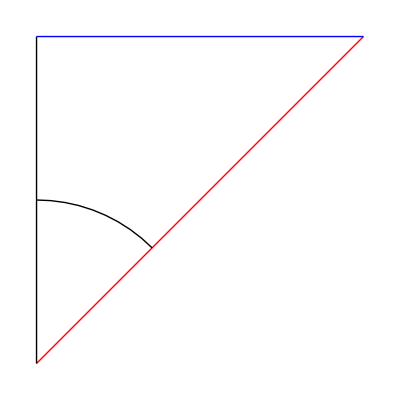

```mathematica
a=Graphics[{Thick,Red,Line[{{0,0},{1,1}}],Thin,Black,Line[{{0,1},{0,0}}],Thick,Blue,Line[{{1,1},{0,1}}],Black,Circle[{0,0},0.5,{Pi/4,Pi/2}]}]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\triangle1.png",a]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\triangle1.png

```mathematica
N@(2*ArcCos[1/(√3)]*180/Pi)
```

109.471

```mathematica
Dot[{1,1,-1},{2,2,0}]/(Length[{1,1,-1}]*Length[{2,2,0}])
```

4/9

```mathematica
ParallelQ
```

```mathematica
MatrixRank[{{1,1,-1},{2,2,0}}]==1
```

False